0.00949267

0.984995

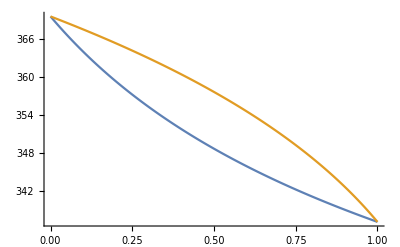

{{0.00949267,0.0287046,96},{0.0264082,0.0773586,95},{0.0438867,0.124519,94},{0.061952,0.170221,93},{0.0806289,0.2145,92},{0.0999437,0.257391,91},{0.119924,0.298929,90},{0.140598,0.339146,89},{0.161995,0.378076,88},{0.184149,0.41575,87},{0.207091,0.452201,86},{0.230856,0.487459,85},{0.255481,0.521555,84},{0.281003,0.554519,83},{0.307464,0.586379,82},{0.334906,0.617166,81},{0.363372,0.646906,80},{0.392909,0.675628,79},{0.423566,0.703359,78},{0.455394,0.730125,77},{0.488448,0.755952,76},{0.522784,0.780865,75},{0.558462,0.80489,74},{0.595545,0.828051,73},{0.6341,0.850372,72},{0.674195,0.871876,71},{0.715905,0.892586,70},{0.759306,0.912524,69},{0.804481,0.931713,68},{0.851514,0.950174,67},{0.900497,0.967928,66},{0.951524,0.984995,65},{1.0047,1.0014,64}}

```mathematica
Clear[Tb,Td]
P=.101325; (*MPa*)
R=8.31447;
ωA=.566;
ωB=.334;
TcA=512.6;
TcB=647.3;
PcA=8.096;
PcB=22.12;

PsatAb=PcA*10^((7/3)*(1+ωA)*(1-1/(Tb/TcA)));
PsatBb=PcB*10^((7/3)*(1+ωB)*(1-1/(Tb/TcB)));
PsatAd=PcA*10^((7/3)*(1+ωA)*(1-1/(Td/TcA)));
PsatBd=PcB*10^((7/3)*(1+ωB)*(1-1/(Td/TcB)));

BubbleT=Tb/.Table[FindRoot[P==PsatAb*xAbub+PsatBb*(1-xAbub),{Tb,200,600}],{xAbub,0,1,.01}];
c=BubbleT-273;
DewT=Td/.Table[FindRoot[P==1/(yAdew/PsatAd+(1-yAdew)/PsatBd),{Td,200,600}],{yAdew,0,1,.01}];
d=DewT-273;
x=Table[x,{x,0,1,.01}];
a=Interpolation[Thread[{c,x}]];
b=Interpolation[Thread[{d,x}]];
a[96]
b[65]

(*Remove the ";" supression below if you want to see ideal Txy diagram*)
ListLinePlot[{BubbleT,DewT},DataRange->{0,1}]
Reverse[Table[Thread[{a[T],b[T],T}],{T,64,96}]]
```